# Broadband Network Congestion Measurement - ICMP ping measurements

How long as TWC been aware of network congestion in High Speed Internet service to Hana, HI?

by Chase.Turner@TFarms.com

For discussion purposes only.  Use of this report requires specific permission of the author.

```mathematica
ClearSystemCache[]
```

## TODO

# Chunk data downloads
Improve response time downloading new measurement data from atlas.ripe.net by annotating file names with indications as to the range of data values included in the data set.  For example : “atlas.ripe.net-measurement-RESULT#-YYYY-MM-DD-T-HH:MM:SSZ - description.json”

# Optional timeline overlay of probe events
When p1178 is displayed, overlay commentary on timeline to draw attention to changes in the data resulting

# Select by IP, result set, etc 
Choice to select all events from a result set, or by IP address cutting across multiple result sets.  Open question what to do about different targets

```mathematica
ipToUser={
{"24.94.68.157","dukewalls@gmail.com","BillW","265 Alalele Pl., Hana, HI 96713"}, 
{"24.94.68.158","razzle@maui.net","Gaylord","290 Kalo Rd, Hana HI 96713"},
{"24.94.68.213","neilhasegawa@me.com", "Neil","5165 Hana Highway, Hana HI 96713"},
{"24.94.69.115", "mardfin@gmail.com","Ward",""},
{"24.94.69.12","HanaFarms@gmail.com", "MartyV Office",""},
{"24.94.69.???","Andrew@hanahawaii.net","Andrew",""},
{"24.94.69.188","robin@hanahawaii.net","Robin Rayner","130 Kalo Road,Hana HI 96713"},
{"24.94.69.215","wrsides@hotmail.com","Bill Sides",""},
{"24.94.69.247","Portofino3@aol.com","Kiran S", ""}, 
{"24.94.69.209","","Bill Church","265 Alalele Pl., Hana, HI 96713"},
{"24.94.69.65","", "RichD",""},
{"29.94.69.???","","RchardP",""},
{"66.27.209.27","","Sky",""},
{"66.27.209.114","mtimbal1945@yahoo.com","Moses",""},
{"205.172.17.95","chase.turner@tfarms.com", "2014-06-06 to 2014-06-10",""},
{"24.94.68.214","chase.turner@tfarms.com","2014-06-10",""}
};
```

Jun 11 2014 02:01:35 TLV - 11 - unrecognized OID; CM - MAC = dc : 45 : 17 : a1 : 25 : ea; CMTS - MAC = 00 : 01 : 5 c : 3 e : 08 : 44; CM - QOS = 1.1; CM - VER = 3.0; 

"'TLV-11 - unrecognized OID' is a harmless error.  It's a conflict with Motorola devices having unsupported SNMP QoS components in our service.  This doesn't mean that anything is necessarily wrong with the service, it just means that the modem cannot fully utilize SNMP services for some reason on that end.  I'm not showing the modem going through any total disconnects, and signals do look good.  If this continues to be an issue, let us know!  We may need to have a technician look into this."

## Terminology

## Events

```mathematica
ClearAll[ probeEvents ];
probeEvents::usage = "Time indexed listing of events pertaining to probes";
probeEvents = { 
{"probe"->p1178, "ts"->DateList["2013-02-01T13:00:00Z"],"event"->"24.94.68.214"},
{"probe"->p1178, "ts"->DateList["2014-06-06T02:41:00Z"],"event"->"205.172.17.95"},
{"probe"->p1178, "ts"->DateList["2014-06-10T02:41:00Z"],"event"->"one bonded channel"},
{"probe"->p1178, "ts"->DateList["2014-06-10T10:41:00Z"],"event"->"Factory Reset; 6 bonded channels"},
{"probe"->p1178, "ts"->DateList["2014-06-10T18:00:00Z"],"event"->"24.94.68.214"}
};
probeEvents//TableForm
```

probe→p1178 | ts→{2013,2,1,13,0,0.} | event→24.94.68.214
probe→p1178 | ts→{2014,6,6,2,41,0.} | event→205.172.17.95
probe→p1178 | ts→{2014,6,10,2,41,0.} | event→one bonded channel
probe→p1178 | ts→{2014,6,10,10,41,0.} | event→Factory Reset; 6 bonded channels
probe→p1178 | ts→{2014,6,10,18,0,0.} | event→24.94.68.214

## Sources

### Display and Legends

#### City where probe is located

```mathematica
ClearAll[cityOfProbe];
Block[{},
cityOfProbe[1165]="Hana";
cityOfProbe[1178]="Hana";
cityOfProbe[15111]="Kahului";
cityOfProbe[2289]="BI:Hawi";
cityOfProbe[12735]="BI:Kailua-Kona";
cityOfProbe[10546]="BI:Hilo";
cityOfProbe[14720]="Ohau:Kaneohe";
];
(* TEST *)
cityOfProbe/@ allProbes
```

{Hana,Hana,Kahului,BI:Hawi,BI:Kailua-Kona,BI:Hilo,Ohau:Kaneohe}

#### Color Scheme for probes

```mathematica
allProbes={1178,1165,15111,2289,12735,10546,14720};
```

```mathematica
ClearAll[colorCodeForProbe];
Block[{},
colorCodeForProbe[1165]=Blue;
colorCodeForProbe[1178]=Red;
colorCodeForProbe[15111]=Purple;
colorCodeForProbe[2289]=Gray;
colorCodeForProbe[12735]=Orange;
colorCodeForProbe[10546]=Pink;
colorCodeForProbe[14720]=Black;
];
```

#### PlotStyle for probe

```mathematica
ClearAll[plotStyleForProbe];
plotStyleForProbe[aProbe_Integer, pSize_, pOpacity_]:=colorCodeForProbe[aProbe];
(* TEST *)
plotStyleForProbe[#,.001,0.5]&/@ allProbes
```

{RGBColor[1,0,0],RGBColor[0,0,1],RGBColor[0.5,0,0.5],GrayLevel[0.5],RGBColor[1,0.5,0],RGBColor[1,0.5,0.5],GrayLevel[0]}

#### Pretty Print for Probe

```mathematica
ClearAll[pprintProbe];
pprintProbe[probe_Integer]:= Style[" p"<>ToString[probe] <> "_"<>cityOfProbe[probe]<>" ",FontColor->colorCodeForProbe[probe], Plain,"Text"];

pprintProbe[probes_List]:= Row[pprintProbe/@ probes];
(* TEST *)
pprintProbe/@ allProbes
```

{ p1178_Hana , p1165_Hana , p15111_Kahului , p2289_BI:Hawi , p12735_BI:Kailua-Kona , p10546_BI:Hilo , p14720_Ohau:Kaneohe }

```mathematica
pprintProbe[ allProbes]
```

p1178_Hana  p1165_Hana  p15111_Kahului  p2289_BI:Hawi  p12735_BI:Kailua-Kona  p10546_BI:Hilo  p14720_Ohau:Kaneohe

### Sources

```mathematica
Clear[pingMeasurements];

pingMeasurements::usage="What measurements to be loaded";

pingMeasurements=If[True,
{
(* Egress Path *)
{1665886,"ping-24.94.68.1 - egress hop1"},

(* transpacific entry point *)
{1664935,"ping-72.129.45.3 - egressToMainland - entry - 7 probes"},
(* Ingress Path *)

(* DNS *)
{1665597,"ping-24.25.227.55 - DNS - TWC"},
{1674540,"ping-24.25.227.55 - DNS - Oceanic"},

(* transpacific crossing *)
{1673158,"ping-104.34.2.250 - egressToMainland - TWC in CA p17329 - 7 probes"},
{1673161,"ping-205.172.17.95 - ingressFromMainland - p17329 to p1178 - 1 probe"},

(* interisland ping to Chase *)
{1604357,"ping-24.94.68.214 - ingressInterislandTo p1178 HanaHouse - 6 probes"},
{1672504,"ping-p1178 - ingressInterislandTo p1178 HanaHouse - 6 probes"},

(* interisland ping to Bill and Marty *)
{1672636,"ping-24.94.69.215 - ingressInterislandTo Bill Sides - 7 probes"},
{1672635,"ping-24.94.69.12 - ingressInterislandTo MartyV Office - 6 probes"}


},
{
(* Egress Path *)
{1665888,"ping-24.25.230.137 - egress hop2"},

(* transpacific entry point *)

(* Ingress Path *)
{1607723,"ping-24.25.230.138 - ingress-hop1"},
{1664937,"ping-72.129.45.79 - ingress-hop2"},
{1664936,"ping-72.129.45.55 - ingress-hop3"},

(* DNS *)

(* transpacific crossing *)
{1604419,"ping-198.45.56.12 - egressToMainland - Netflix - 7 probes"},

(* interisland ping in *)
{1604357,"ping-24.94.68.214 - ingressInterislandTo HanaHouse - ending 20140606"}

}]
```

{{1665886,ping-24.94.68.1 - egress hop1},{1664935,ping-72.129.45.3 - egressToMainland - entry - 7 probes},{1665597,ping-24.25.227.55 - DNS - TWC},{1674540,ping-24.25.227.55 - DNS - Oceanic},{1673158,ping-104.34.2.250 - egressToMainland - TWC in CA p17329 - 7 probes},{1673161,ping-205.172.17.95 - ingressFromMainland - p17329 to p1178 - 1 probe},{1604357,ping-24.94.68.214 - ingressInterislandTo p1178 HanaHouse - 6 probes},{1672504,ping-p1178 - ingressInterislandTo p1178 HanaHouse - 6 probes},{1672636,ping-24.94.69.215 - ingressInterislandTo Bill Sides - 7 probes},{1672635,ping-24.94.69.12 - ingressInterislandTo MartyV Office - 6 probes}}

#### fetchJSONMeasurement

```mathematica
ClearAll[fetchJSONMeasurement];
Needs["JLink`"];
fetchJSONMeasurement[resultNumber_Integer, friendlyName_String]:=Module[
{defaultCacheDir, fullPathToCache,uri, jsonData},
defaultCacheDir=FileNameJoin[{NotebookDirectory[], "data"}];
fullPathToCache=FileNameJoin[{defaultCacheDir,"RIPE-Atlas-measurement-"<>ToString[resultNumber]<>"-"<>friendlyName<>".json"}];
uri="https://atlas.ripe.net/api/v1/measurement/"<>ToString[resultNumber]<>"/result";

(* PREPARE JSON PARSER FOR LARGE FILES  *)
InstallJava[];
ReinstallJava[CommandLine->"java",JVMArguments->"-Xmx2024m"];

If[FileExistsQ[fullPathToCache],
jsonData=Import[fullPathToCache,"JSON"],
Module[{},
jsonData=Import[uri,"JSON"];
Export[fullPathToCache,jsonData,"JSON"]];
(* CLEAN UP JSON PARSER *)
UninstallJava[];
(* --->RETURNING *)
jsonData
]
];

(* TEST *)
If[False,fetchJSONMeasurement/@ pingMeasurements,Message["Test skipped; did not load JSON files"]];
```

Message::name: Message name "Test skipped; did not load JSON files" is not of the form symbol::name or symbol::name::language.

### Selected Data

```mathematica
(* tPingData *)
ClearAll[tPingData];
tPingData::usage="Organize entires here to reflect traceroute path";
```

```mathematica
tPingData=Flatten[fetchJSONMeasurement[#[[1]],#[[2]]]&/@ pingMeasurements,1];
(* TEST *)
{Dimensions[#,Depth[#]], Depth[#],LeafCount[#]}&/@ {tPingData}
```

{{{348061},7,34978168}}

### Transcode

#### Conversion of Unix Machine Timestamp to MathematicaTime

```mathematica
ClearAll[unixTimeToHST];
unixTimeToHST::usage="Given a atlas.ripe.net timestamp, convert to Unix time and adjuat to HST";
(* MESSAGES *)
unixTimeToHST::unexpectedArgument["`1`"];
(* IMPLEMETATION *)
(* Hawaiian Timezone is -10 from GMT *)
unixTimeToHST[x_Integer]:=DateList[AbsoluteTime[{1970,1,1,2,0,0}]+x,TimeZone->-10.0];
(* UNEXPECTED ARGUMENTS *)
unixTimeToHST[x_]:=Message[unixTimeToHST::unexpectedArgument,x];
(* TEST *)
unixTimeToHST[1330434000]
{2012,2,28,10,0,0.}
```

{2012,2,28,10,0,0.}

{2012,2,28,10,0,0.}

#### Verify : result types are known

Purpose of this section is to verify result types and values are known -- by a process of elimination.

Strategy: Collect results, and then specify patterns and delete.  The result should be an empty set.

```mathematica
ClearAll[results];
results::usage="Holds timing results";
results::unknownPattern="An unknown pattern was detected";
results::patternsVerified="All results matched known patterns";
results="result"/. tPingData;
```

```mathematica
ClearAll[pNormal,pDup1,pDup2,pUnreachable,pUnreachable2,pAllPatterns];
pNormal={"rtt"->rtt_}|{"rtt"->rtt_,"ttl"->_Integer};
pDup1={"dup"->_Integer,"rtt"->rtt_};
pDup2={"dup"->_Integer,"rtt"->rtt_,"ttl"->_Integer};
pUnreachable={"srcaddr"->ipAddr_String, "x"->"*"};
pUnreachable2={"x"->"*"};
pAllPatterns={pNormal,pDup1,pDup2,pUnreachable,pUnreachable2};
(* VERIFY *)
Block[{resultsWithUnknownValues},
resultsWithUnknownValues=DeleteCases[DeleteCases[#,Alternatives@@pAllPatterns]&/@results,{}];
If[Length[resultsWithUnknownValues]>0,
Message[results::unknownPattern], 
results::patternsVerified]]
```

results::unknownPattern: An unknown pattern was detected

#### Transcode JSON data to CDF

```mathematica
ClearAll[resultsToCDF];
(* MESSAGES *)
resultsToCDF::usage="Convert the JSON data into CDF Array";
resultsToCDF::unexpectedArg="`1`";

(* IMPLEMENTATION *)
resultsToCDF[aJSONResults_List]:= Block[{rtts, dropped},
rtts="rtt"/. Cases[aJSONResults,pNormal];
(* FIXME - what should be done with the DUP matches?  At present, they are ignored *)
dropped=Cases[aJSONResults,pUnreachable|pUnreachable2];
(* ---> RETURNING *)
{rtts,dropped}
];
(* UNEXPECTED ARGUMENT *)
resultsToCDF[x_]:=Message[resultsToCDF::unexpectedArg,x];

ClearAll[jsonToCDF];
(* MESSAGES *)
jsonToCDF::usage="Convert the JSON data into CDF Array";
jsonToCDF::unexpectedArg="`1`";

(* IMPLEMENTATION *)
jsonToCDF[aJSON_List]:= Block[{convertedData},
convertedData={"prb_id","dst_addr","sent","timestamp","result"}/.#&/@aJSON;
Join[#[[1;;3]],{unixTimeToHST[#[[4]]]},resultsToCDF[#[[5]]]]&/@ convertedData
];

jsonToCDF[aResult_String]={{},0};

(* UNEXPECTED ARGUMENT *)
jsonToCDF[x_]:=Message[jsonToCDF::unexpectedArg,x];

(* TEST *)
Length[tPingDataCDF=jsonToCDF[tPingData]]
```

348061

#### Result Summary Types

```mathematica
rttMean::usage="Mean value";
rttMean5pct::usage="Mean of RTTs after dropping 5% of smallest and largest elements";
rttMean95pct::usage="Mean of RTTs after dropping 95% of smallest and largest elements";
rttMax::usage="Maximum RTT value from the set";
rttMin::usage="Minimum RTT value from the set";
rttMean[rtt_List]:=Mean[rtt];
rttMean95pct[rtt_List]:=TrimmedMean[rtt,0.05];
rttMean5pct[rtt_List]:=TrimmedMean[rtt,0.45];
rttMax[rtt_List]:=Max[rtt];
rttMin[rtt_List]:=Min[rtt];
```

#### Accessor Functions

```mathematica
ClearAll[targetsIn];

targetsIn[tData_List]:=
DeleteDuplicates[Cases[tData,{
prbID_Integer,
target_String,
sent_Integer,
timestamp_,
rttList_List,
dropped_List
}:>target]
];
(* TEST *) 
targetsIn[tPingDataCDF]
```

{24.94.68.1,72.129.45.3,24.25.227.55,205.172.19.79,104.34.2.250,205.172.17.95,24.94.68.214,24.94.69.215,24.94.69.12}

```mathematica
probesIn[tData_List]:=
DeleteDuplicates[Cases[tData,{
prbID_Integer,
target_String,
sent_Integer,
timestamp_,
rttList_List,
dropped_List
}:>prbID]
];
(* TEST *) 
probesIn[tPingDataCDF]
```

{1165,1178,14720,2289,10546,15111,12735,17329}

```mathematica
ClearAll[selectByHours];

selectBy[tData_List,probes_List,targetIP_String]:=Cases[tData,
{
prbID_Integer,
target_String,
sent_Integer,
timestamp_,
rttList_List,
dropped_List
}/; And[
MemberQ[probes,prbID] , 
StringMatchQ[target,targetIP]]
];
(* TEST *)
Length[selectBy[tPingDataCDF,{1165},"24.94.68.1"]]
```

7947

```mathematica
selectBy[tData_List,probes_List,targetIPs_List]:=Cases[tData,
{
prbID_Integer,
target_String,
sent_Integer,
timestamp_,
rttList_List,
dropped_List
}/; And[
MemberQ[probes,prbID] , 
StringMatchQ[target,Alternatives@@targetIPs]]
];
(* TEST *)
Length[selectBy[tPingDataCDF,{1165},{"24.94.68.214","205.172.17.95"}]]
```

25314

```mathematica
ClearAll[selectByHours];

selectByHours[tData_List,probes_List,targetIP_String,hours_List]:=Cases[tData,
{
prbID_Integer,
target_String,
sent_Integer,
timestamp_,
rttList_List,
dropped_List
}/; And[
MemberQ[probes,prbID] , 
StringMatchQ[target,targetIP],
MemberQ[hours,timestamp[[4]]]]
];
(* TEST *)
Length[selectByHours[tPingDataCDF,{1165},"24.94.68.1",{1}]]
```

330

```mathematica
Clear[selectByTimeSlice];

selectByTimeSlice[tData_List,probes_List,targetIP_String,timeSlice_List]:=Cases[tData,
{
prbID_Integer,
target_String,
sent_Integer,
timestamp_,
rttList_List,
dropped_List
}/; And[
MemberQ[probes,prbID] , 
StringMatchQ[target,targetIP],
AbsoluteTime[timeSlice[[1]]]≤ AbsoluteTime[timestamp] ≤AbsoluteTime[timeSlice[[2]]]
]
];
(* TEST *)
Length[selectByTimeSlice[tPingDataCDF,{1165},"24.94.68.1",{{2014,5,19,11},{2014,5,19,12}}]]
```

15

```mathematica
ClearAll[rttDateListPlot];

rttDateListPlot[tData_List,probes_List,targetIP_String]:=
Block[{matches,timeAndRtt,timeAndDropCount},
matches=selectBy[tData,probes,targetIP];
timeAndRtt=
{
{#[[4]],rttMin[#[[5]]]}&/@matches,
{#[[4]],rttMean5pct[#[[5]]]}&/@matches,
{#[[4]],rttMax[#[[5]]]}&/@matches,
{#[[4]],-Length[#[[5]]]}&/@matches
}
;

DateListPlot[
timeAndRtt,
PlotRange->{Automatic,{-17, 100}},
Joined->True,
ImageSize->Medium,
PlotLabel->StringForm["`1` RTT to `2`",pprintProbe[probes],targetIP,FontColor->Black, Plain,"Text" ]
]
];

rttDateListPlot[tData_List,probes_List,targetIPs_List]:=
Block[{matches,timeAndRtt,timeAndDropCount},
matches=selectBy[tData,probes,targetIPs];
timeAndRtt=
{
{#[[4]],rttMin[#[[5]]]}&/@matches,
{#[[4]],rttMean5pct[#[[5]]]}&/@matches,
{#[[4]],rttMax[#[[5]]]}&/@matches,
{#[[4]],-Length[#[[5]]]}&/@matches
}
;

DateListPlot[
timeAndRtt,
PlotRange->{Automatic,{-17, 100}},
Joined->True,
ImageSize->Medium,
PlotLabel->StringForm["`1` RTT to `2`",pprintProbe[probes],targetIPs,FontColor->Black, Plain,"Text" ]
]
];
```

## Egress

### 24.94.68.1 - 1st Hop out for Hana on RoadRunner Routes

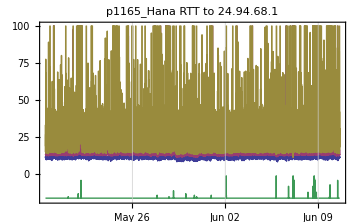
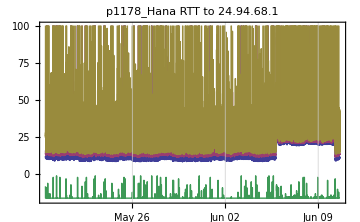

```mathematica
Table[rttDateListPlot[tPingDataCDF,probe,"24.94.68.1"],{probe, {{1165},{1178}}}]
```

### 24.94.68.1 - 1st Hop out for Hana on Oceanic Routes

```mathematica
If[False,Table[rttDateListPlot[tPingDataCDF,probe,"24.94.68.1"],{probe, {{1165},{1178}}}],{}]
```

{}

### 24.25.230.137 - 2nd Hop out for Hana RoadRunner Routes

```mathematica
If [False,Table[rttDateListPlot[tPingDataCDF,probe,"24.25.230.137"],{probe, {{1165},{1178}}}],{}]
```

{}

### 72.129.45.3 - Transpacific Entry Point

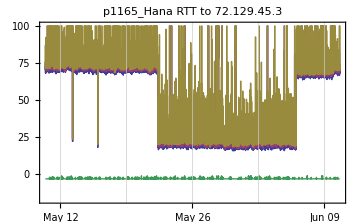
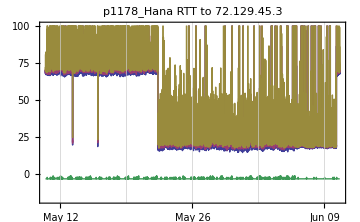

```mathematica
Table[rttDateListPlot[tPingDataCDF,probe,"72.129.45.3"],{probe, {{1165},{1178}}}]
```

```mathematica
If[False,Table[rttDateListPlot[tPingDataCDF,probe,"72.129.45.3"],{probe, {{1165,1178},{15111},{2289},{10546},{12735},{14720}}}], {}]
```

{}

### 198.45.56.12 - Netflix - San Jose

```mathematica
If[False,Table[rttDateListPlot[tPingDataCDF,probe,"198.45.56.12"],{probe, {{1165,1178},{15111},{2289},{10546},{12735},{14720}}}],{}]
```

{}

### 104.34.2.250 - TWC CA p17329

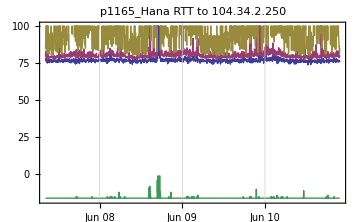
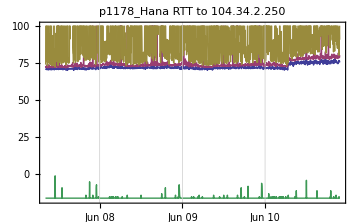
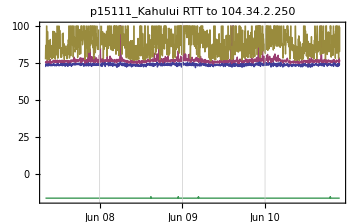
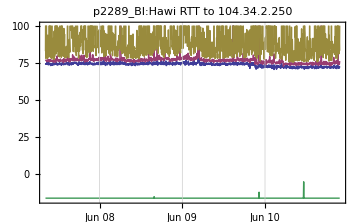
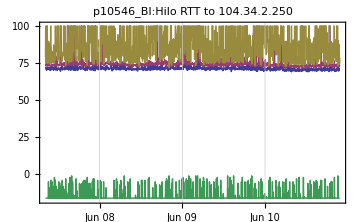
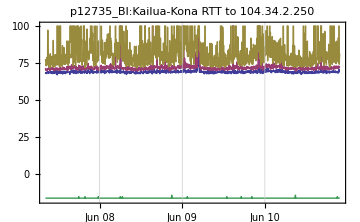
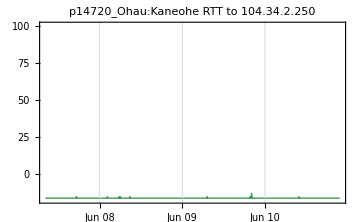

```mathematica
If[True,Table[rttDateListPlot[tPingDataCDF,probe,"104.34.2.250"],{probe, {{1165},{1178},{15111},{2289},{10546},{12735},{14720}}}],{}]
```

## Ingress

### 24.25.230.138 - Last hop before landing at Hana

```mathematica
If[False,Table[rttDateListPlot[tPingDataCDF,probe,"24.25.230.138"],{probe, {{1165,1178},{15111},{2289},{10546},{12735},{14720}}}],{}]
```

{}

### 72.129.45.79 - 2nd to Last Hop before landing at Hana

```mathematica
If[False,Table[rttDateListPlot[tPingDataCDF,probe,"72.129.45.79"],{probe, {{1165,1178},{15111},{2289},{10546},{12735},{14720}}}],{}]
```

{}

### 72.129.45.55 - Hop delivering to Hana and Kehei

```mathematica
If[False,Table[rttDateListPlot[tPingDataCDF,probe,"72.129.45.55"],{probe, {{1165,1178},{15111},{2289},{10546},{12735},{14720}}}],{}]
```

{}

### Ping Chase’s house ( 24.94.68.214 , 205.172.17.95 )

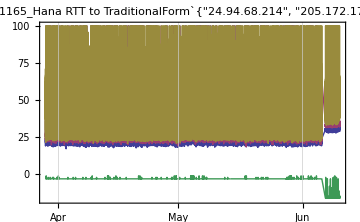
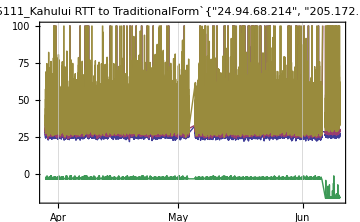
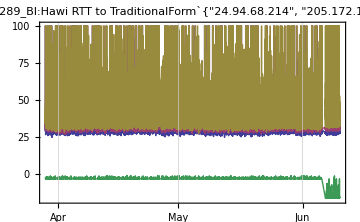
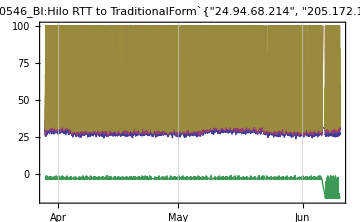
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
If[True,Table[rttDateListPlot[tPingDataCDF,probe,{"24.94.68.214","205.172.17.95"}],{probe, {{1165},{15111},{2289},{10546},{12735},{14720}}}],{}]
```

### Ping Marty’s office ( 24.94.69.12 )

```mathematica
If[False,Table[rttDateListPlot[tPingDataCDF,probe,"24.94.69.12"],{probe, {{1165},{15111},{2289},{10546},{12735},{14720}}}],{}]
```

{}

### Ping Bill’s house ( 24.94.69.225 )

```mathematica
If[True,Table[rttDateListPlot[tPingDataCDF,probe,"24.94.69.215"],{probe, {{1165},{1178},{15111},{2289},{10546},{12735},{14720}}}],{}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## DNS

### 24.25.227.55 - DNS

```mathematica
Table[rttDateListPlot[tPingDataCDF,probe,"24.25.227.55"],{probe, {{1165},{1178},{15111},{2289},{10546},{12735},{14720}}}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
If[False,Table[rttDateListPlot[tPingDataCDF,probe,"24.25.227.55"],{probe, {{1165,1178},{15111},{2289},{10546},{12735},{14720}}}],{}]
```

{}

```mathematica
Table[rttDateListPlot[tPingDataCDF,probe,"205.172.19.79"],{probe, {{1165},{1178},{15111},{2289},{10546},{12735},{14720}}}]
```

DateListPlot::ntdt: The first argument to DateListPlot should be a list of pairs of dates and real values, a list of real values, or a list of several such lists.

{-Graphics-,-Graphics-,DateListPlot[{{},{},{},{}},PlotRange→{Automatic,{-17,100}},Joined→True,ImageSize→Medium,PlotLabel→ p15111_Kahului  RTT to 205.172.19.79],-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## SCRATCH